```mathematica
unet[uin_,αf_,f_]:= uin -αf f
f[unet_,τm_,tref_,xt_]:=1/(tref-τm Log[1-xt/unet])
```

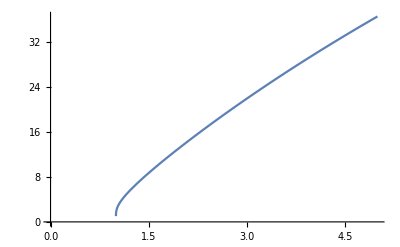

```mathematica
fu[unet_]:=1/(tref-τm Log[1-xt/unet])
Plot[fu[uin]/.{τm->0.1,tref->0.005,xt->1},{uin,0,5}]
```

Test for how to use DSolve

```mathematica
Integrate[1/(-x+5),x]
```

-log(5-x)

```mathematica
DSolve[x'[t]==-x[t]+5,x[t],t]
```

{{x(t)→c_1 ⅇ^-t+5}}

Use DSolve to see if we can get and analytical form for the mathematical model of an adaptive neuron

```mathematica
DSolve[{τ ft'[t]==(ft[t])^2(uft[t]-α ft[t]),τf uft'[t]==-uft[t]+αft[t],ft[0]==fu[3],uft[0]==0},{ft[t],uft[t]},t]
```

DSolve[{τ ft'(t)==(ft(t))^2 (uft(t)-α ft(t)),τf uft'(t)==αft(t)-uft(t),ft(0)==21.9556,uft(0)==0},{ft(t),uft(t)},t]

We can’t :-(

h[t] is the impulse response of a synapse.  It essentially shows what happens when you pass in an impulse to a low-pass filter.  Why do we divide by τ_syn?

```mathematica
h[t_]:=Exp[-t/τsyn]/τsyn UnitStep[t]
```

Define the piecewise formula for the linear approximation of the rate-mode adaptation neuron

```mathematica
g[t_]:=Piecewise[{{dfdt t+ f0,0<=t<tss},{fss,t≥tss}},0]
g[t]
```

Piecewise[{{dfdt t+f0, 0≤t<tss}, {fss, t≥tss}}]

a[t] is defined as a[t]=h[t]*g[t]

```mathematica
a[t_]=FullSimplify[Refine[Convolve[h[y],g[y],y,t],t>0 &&ssTime>0]]
```

Piecewise[{{fss-fss ⅇ^((tss-t)/τsyn), t>tss∧tss≤0}, {ⅇ^(-t/τsyn) (dfdt τsyn-f0)+dfdt t-dfdt τsyn+f0, t≤tss}, {ⅇ^(-t/τsyn) (-ⅇ^(tss/τsyn) (-dfdt tss+dfdt τsyn+fss)+dfdt τsyn+f0 (ⅇ^(tss/τsyn)-1)+fss ⅇ^(t/τsyn)), True}}]

```mathematica
Manipulate[
Plot[{
g[t]/.{tss->(ssF-initF)/dfdt}/.{τsyn->tauSyn,f0->initF,dfdt->slopeApprox,fss->ssF},
a[t]/.{tss->(ssF-initF)/dfdt}/.{τsyn->tauSyn,f0->initF,dfdt->slopeApprox,fss->ssF},
ssF(1-ⅇ^(-t/tauSyn)),
ssF},
{t,0,5},PlotRange->All],
{{slopeApprox,-25},-50,0},
{{initF,100},0,100},
{{ssF,50},0,100},
{{tauSyn,0.5},0,1}
]
```

## Scratch Pad